# Notes on Beer’s analysis of CTRNN (and Homeo parallels)

## Equation for one Homeo unit with no input

The following is the equation for oneHomeo unit with no input, with m = mass, v = viscosity, w = weight of self connection. The equation is entered into the EquationTrekker to expore its dynamics.

```mathematica
<<EquationTrekker`
```

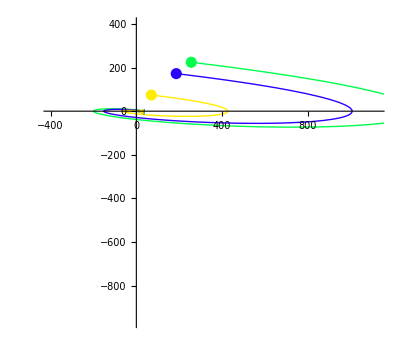
{EquationTrekkerState["myx0100","{m → 94.0001, v → 10., w → 1.}",TrekData["0.y'", <>]
TrekData["0.y'", <>]
TrekData["0.y'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[m*y''[x] == -v*y'[x]-w*y[x] ,y,{x,0, 100},
PlotRange -> {{-400,400},{-400,400}},
TrekParameters->{v->{0,{-10,10}},
w->{1,{-1,1}},
m->{1,{0.001,100}}}]
```

Here we add a constant external input i

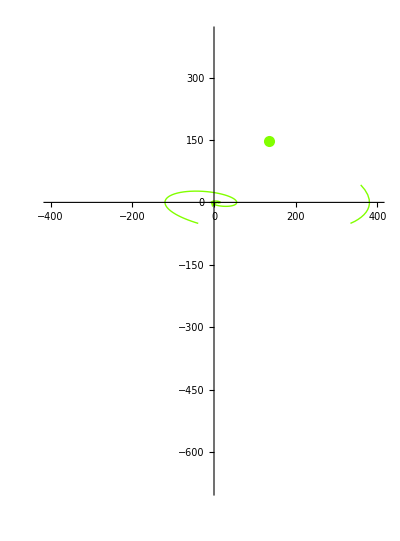
{EquationTrekkerState["myx0100","{i → 1., m → 1., v → 0.2, w → 0.1}",TrekData["0.y'", <>], <>],-Graphics-}

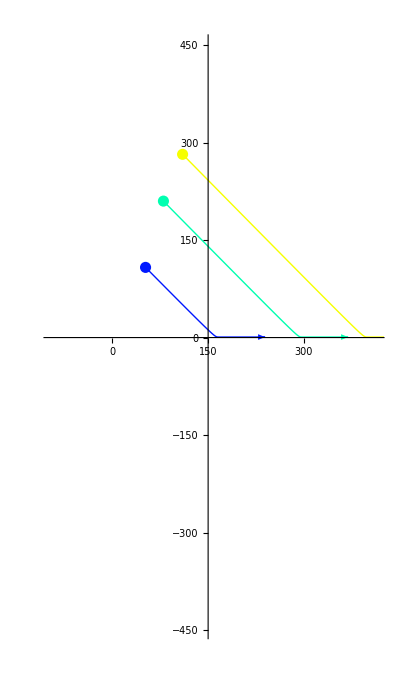
{EquationTrekkerState["myx0100","{i → 0.8, m → 1., v → 1., w → 0.}",TrekData["0.y'", <>]
TrekData["0.y'", <>]
TrekData["0.y'", <>], <>],-Graphics-}

```mathematica
EquationTrekker[m*y''[x] == -v*y'[x]-w*y[x]+i ,y,{x,0, 100},
PlotRange -> {{-400,400},{-400,400}},
TrekParameters->{v->{0,{-10,10}},
w->{1,{-1,1}},
m->{1,{0.001,100}},
i->{1,{-10,10}}}]
```

```mathematica
res[v_,c1_,c2_]:=DSolve[{x''[t]==-v*x'[t],x'[0]==c2,x[0]==c1},x[t],t]
```

```mathematica
Plot[res[1,1,1],{t,-1,1}]
```

DSolve::dsvar: -0.999959 cannot be used as a variable.

DSolve::dsvar: -0.959143 cannot be used as a variable.

General::stop: Further output of DSolve :: dsvar will be suppressed during this calculation.

-Graphics-

Here we solve the second-order differential equation (with added constant input), and initial conditions  for position: y(0)  and for velocity: y’(0):

DSolve[{m y''[x]==i-w y[x]-v y'[x],True},y[x],x]

```mathematica
h=DSolve[{m*x''[t]+v*x'[t]+w*x[t]-i==0,x[0]==c1,x'[0]==c2},x[t],t]
```

{{x[t]→1/(2 w √(v^2-4 m w))(ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) i v-ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) i v-2 c2 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) m w+2 c2 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) m w-c1 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) v w+c1 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) v w+2 i √(v^2-4 m w)-ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) i √(v^2-4 m w)-ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) i √(v^2-4 m w)+c1 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) w √(v^2-4 m w)+c1 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) w √(v^2-4 m w))}}

{{x[t]→1/(2 w √(v^2-4 m w))(ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) i v-ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) i v-2 c2 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) m w+2 c2 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) m w-c1 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) v w+c1 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) v w+2 i √(v^2-4 m w)-ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) i √(v^2-4 m w)-ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) i √(v^2-4 m w)+c1 ⅇ^((t (-v-√(v^2-4 m w)))/(2 m)) w √(v^2-4 m w)+c1 ⅇ^((t (-v+√(v^2-4 m w)))/(2 m)) w √(v^2-4 m w))}}

and then we plot the results with a manipulator:

```mathematica
Manipulate[Plot[h,
				{t,-10,10},
				PlotRange->Automatic,
				AspectRatio-> 1,AxesLabel->{t,x}],
		{{i,0,"i: Constant input"},-10,10,Appearance->"Labeled"},
		{{w,0.11,"w: weight"},0.01,1,Appearance->"Labeled"},
		{{v, 10,"viscosity"},0,100,Appearance ->"Labeled"},
		{{m,10,"m: mass"},0.001,1003,Appearance->"Labeled"},
		{{c1,0,"c1: integr const"},0,100,Appearance->"Labeled"},
		{{c2,0,"m: integr const"},0,100,Appearance->"Labeled"},
	ControlPlacement->Left]
```

[For some reasons I  cannot get Mathematica to plot the results, even though the equation seems correct. But briefly, we have a harmonic oscillator if v > 0, and the oscillator is damped if w > 0. With v <0, we no longer have an oscillator, but an exponentially growing function. Similarly, if v=0 and w>0.
In absence of a self-connection, the equation reduces to an exponential (or more than exponential?) decay to I, while in the absence of v, it reduces to a harmonic oscillator. If both v and w  are > 0, we have a damped oscillator with a constant input. The fixed point will be the input I (or an expression of I ?? check). If we add uniselector action, with both v and w we see that nothing changes, as the damped oscillator would always goes back to equilibrium (no matter how fast or slow).

### Equilibrium points